2. kolokvij DISMOD, 4. 5. 2018, študent Jakob Valič

### 1. naloga

```mathematica
opravila=({{180, 255, 45, 120, 30, 270}, {195, 255, 300, 300, 90, 105}, {180, 270, 270, 135, 30, 60}, {135, 150, 75, 300, 195, 255}});
{m,n}=Dimensions[opravila];
```

```mathematica
(X=Table[Subscript[x, i,j],{i,m},{j,n}])//MatrixForm;
```

```mathematica
kriterijskaFn=Plus@@Flatten[opravila*X];
pogojOpravila=Plus@@#==1&/@X;
pogojDelavci=Plus@@#<=1&/@Transpose[X];
pogojNenegativnost=#≥0&/@Flatten[X];
```

```mathematica
resitev=Minimize[Join[
{kriterijskaFn,
pogojDelavci,
pogojOpravila,
pogojNenegativnost}
],
Flatten[X],
Integers
];
najmanjsiCas=resitev⟦1⟧
```

315

```mathematica
(prireditev=X/.resitev⟦2⟧)//MatrixForm
```

(0 | 0 | 1 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 1
0 | 0 | 0 | 0 | 1 | 0
1 | 0 | 0 | 0 | 0 | 0)

Odgovor: Delavec 1 dobi delo D, delavec 3 delo A, delavec 5 delo C in delavec 6 delo B.

### 2. naloga

```mathematica
strosekSkladisce=({{70, 60}, {40, 50}});
strosekKupec=({{60, 70, 70}, {70, 80, 50}});
```

```mathematica
{mSkladisce,nSkladisce}=Dimensions[strosekSkladisce];
XSkladisce=Table[Subscript[y, i,j],{i,mSkladisce},{j,nSkladisce}];
{mKupec,nKupec}=Dimensions[strosekKupec];
XKupec=Table[Subscript[z, i,j],{i,mKupec},{j,nKupec}];
```

```mathematica
kriterijskaFnPodjetje=Plus@@Flatten[strosekSkladisce*XSkladisce]+Plus@@Flatten[strosekKupec*XKupec];
pogojTovarne=Plus@@#==300&/@XSkladisce;
pogojKupci=Plus@@#==200&/@Transpose[XKupec];
vsotaSkladiscaIzTovarn=Plus@@#&/@Transpose[XSkladisce];
vsotaSkladiscaDoKupcev=Plus@@#&/@XKupec;
pogojSkladisca={Subscript[y, 1,1]+Subscript[y, 2,1]==Subscript[z, 1,1]+Subscript[z, 1,2]+Subscript[z, 1,3],Subscript[y, 1,2]+Subscript[y, 2,2]==Subscript[z, 2,1]+Subscript[z, 2,2]+Subscript[z, 2,3]};
pogojNenegativnostTovarna=#≥0&/@Join[Flatten[XSkladisce],Flatten[XKupec]];
```

```mathematica
resitevPodjetje=Minimize[Join[
{kriterijskaFnPodjetje,
pogojTovarne,
pogojKupci,
pogojSkladisca,
pogojNenegativnostTovarna}
],
Join[Flatten[XKupec], Flatten[XSkladisce]],
Integers
]
```

{67000,{z_(1,1)→200,z_(1,2)→200,z_(1,3)→0,z_(2,1)→0,z_(2,2)→0,z_(2,3)→200,y_(1,1)→100,y_(1,2)→200,y_(2,1)→300,y_(2,2)→0}}

```mathematica
najnizjiPrevozniStrosek=resitevPodjetje⟦1⟧
```

67000

```mathematica
(XSkladisce/.resitevPodjetje⟦2⟧)//MatrixForm
```

(100 | 200
300 | 0)

Najbolj se nam splača iz prve tovarne peljati 100 ton v prvo skladišče in 200 ton v drugo skladišče. Iz druge tovarne prepeljemo vseh 300 ton v prvo skladišče.

```mathematica
(XKupec/.resitevPodjetje⟦2⟧)//MatrixForm
```

(200 | 200 | 0
0 | 0 | 200)

Odgovor: Iz prvega skladišča peljemo 200 ton do prvega kupca in 200 ton do drugega kupca. Iz drugega skladišča peljemo 200 ton do tretjega kupca.

## 3. naloga

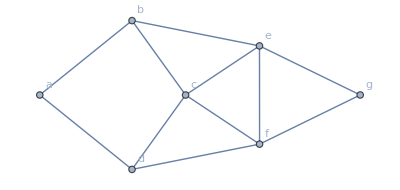

```mathematica
𝒢 =UndirectedGraph[{
a->d,a->b,
b->e,b->c,
c->d,c->e,c->f,
d->f,
e->g,e->f,
f->g} ,VertexLabels->"Name"]
```

Dodati moramo še VertexCapacity→{4,6,3,7,3,9,2,9,3,8,5}.
Nato nalogo poskusimo rešiti s FindMaximumFlow, s tem, da menjujemo začena in končna vozlišča. Lahko kar s Table namesto z zanko. Izberemo tisti par vozlišč, pri katerih bo vrednost največja.